```mathematica
s[t_,ω_,ϕ_]:=Sin[2π ω t + ϕ]
s[t_,ω_]:=s[t,ω,0]
c[t_,ω_,ϕ_]:=Cos[2π ω t + ϕ]
c[t_,ω_]:=c[t,ω,0]
e[t_,ω_,ϕ_]:=Exp[ⅈ (2π ω t + ϕ)]
e[t_,ω_]:=e[t,ω,0]
```

```mathematica
Integrate[e[t,n1 ω]e[t,-n2 ω],{t,0,1/ω}]
FullSimplify[%,Assumptions->n1∈Integers&&n2∈Integers]
```

-(ⅈ (-1+ⅇ^(2 ⅈ (n1-n2) π)))/(2 (n1-n2) π ω)

0

```mathematica
Simplify[Integrate[c[t,n ω]^2,{t,0,1/ω}],n∈Integers]
```

1/(2 ω)

```mathematica
Plot[Abs[e[t,1,0]+e[t,1,1.2]]^2,{t,0,4}]
```

-Graphics-

```mathematica
FullSimplify[2Re[e[t,ω1]e[t,-ω2]],ϕ∈Reals&&t∈Reals&&ω1∈Reals&&ω2∈Reals]
```

2 Cos[2 π t (ω1-ω2)]

```mathematica
TrigExpand[s[t,ω1]s[t,ω2]]
```

4 Cos[π t ω1] Cos[π t ω2] Sin[π t ω1] Sin[π t ω2]

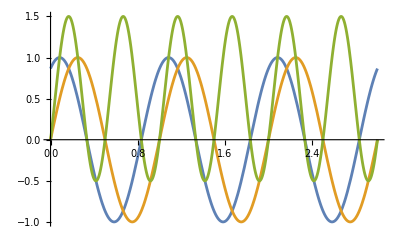

```mathematica
Plot[{s[t,1,π/3],s[t,1],2s[t,1,π/3]s[t,1]},{t,0,3}]
```

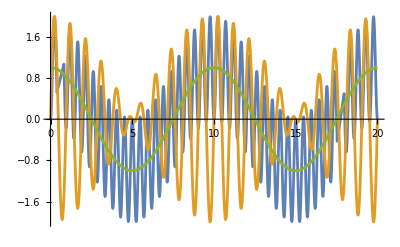

```mathematica
Plot[{2s[t,1.1]s[t,1],s[t,1.1]+s[t,1],c[t,0.1]},{t,0,20}]
```

```mathematica
Series[Cos[x],{x,0,2}]
```

1-x^2/2+O[x]^3